# Infinite 3D medium, Isotropic Point Source, Rayleigh Scattering

## Chi-3 Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine

### Namespace

```mathematica
Begin["inf3DisopointRayleighscatterChi3`"]
```

inf3DisopointRayleighscatterChi3`

## Analytical results

### Collision rate density

collision rate density Cc due to correlated emission:

#### derivation

```mathematica
Clear[cpc,c];
cpc[s_]:=c(ⅇ^(-s^2/4) s^2)/(2 √π)
```

```mathematica
f00=Fpc[0,0,cpc,u];
f10=Fpc[1,0,cpc,u];
f11=Fpc[1,1,cpc,u];
f20=Fpc[2,0,cpc,u];
f22=Fpc[2,2,cpc,u];
```

```mathematica
o=3;
Clear[A,b,c,r,h,F];
A[n_]:=0;
A[0]:=1;
A[1]:=0;
A[2]:=1/2;
hsystem=Table[h[k]==2/Pi u F[k,0]+ Sum[A[m]h[m]F[k,m],{m,0,o-1}],{k,0,o-1}];
hsystemsolve=Simplify[Solve[hsystem,Table[h[i],{i,0,o-1}]]/.F[0,0]->f00/.F[0,1]->-f10/.F[1,1]->f11/.F[1,0]->f10/.F[2,0]->f20/.F[0,2]->f20/.F[2,2]->f22]
```

{{h[0]→(2 c u (8 u^2 (9 c-4 ⅇ^(u^2) u^4)+18 c ⅇ^(u^2) √π u (-1+2 u^2) Erf[u]-9 c ⅇ^(2 u^2) π Erf[u]^2))/(π (-4 u^2 (18 c^2+8 ⅇ^(2 u^2) u^4-3 c ⅇ^(u^2) (9+4 u^2+4 u^4))+6 c ⅇ^(u^2) √π u (c (3-6 u^2)+ⅇ^(u^2) (-9+2 u^2)) Erf[u]+9 c^2 ⅇ^(2 u^2) π Erf[u]^2)),h[1]→(4 c ⅇ^(u^2) ((1+2 u^2) DawsonF[u] (-16 ⅇ^(u^2) u^5+c (54 u+24 u^3+8 u^5)+3 c ⅇ^(u^2) √π (-9+2 u^2) Erf[u])+u (-2 c u (27+12 u^2+4 u^4)-3 ⅇ^(u^2) √π Erf[u] (c (-9+2 u^2)+2 √π u^3 F[1,2])+4 u^4 (4 ⅇ^(u^2) u+√π (3+2 u^2) F[1,2]))))/(π^(3/2) (-4 u^2 (18 c^2+8 ⅇ^(2 u^2) u^4-3 c ⅇ^(u^2) (9+4 u^2+4 u^4))+6 c ⅇ^(u^2) √π u (c (3-6 u^2)+ⅇ^(u^2) (-9+2 u^2)) Erf[u]+9 c^2 ⅇ^(2 u^2) π Erf[u]^2)),h[2]→-((16 c ⅇ^(u^2) u^4 (-6 u-4 u^3+3 ⅇ^(u^2) √π Erf[u]))/(π (-4 u^2 (18 c^2+8 ⅇ^(2 u^2) u^4-3 c ⅇ^(u^2) (9+4 u^2+4 u^4))+6 c ⅇ^(u^2) √π u (c (3-6 u^2)+ⅇ^(u^2) (-9+2 u^2)) Erf[u]+9 c^2 ⅇ^(2 u^2) π Erf[u]^2)))}}

```mathematica
Clear[r,c];First[(2k+1)1/(4 Pi c)(h[k])u SphericalBesselJ[k,r u]/.k->0/.hsystemsolve//FullSimplify]
```

(u (72 c u^2-9 c ⅇ^(2 u^2) π Erf[u]^2-2 ⅇ^(u^2) u (16 u^5+9 c √π (1-2 u^2) Erf[u])) Sin[r u])/(2 π^2 r (-72 c^2 u^2-6 c ⅇ^(u^2) u (-2 u (9+4 (u^2+u^4))+3 c √π (-1+2 u^2) Erf[u])+ⅇ^(2 u^2) (-32 u^6+6 c √π u (-9+2 u^2) Erf[u]+9 c^2 π Erf[u]^2)))

#### result

```mathematica
Ccexact[r_,c_]:=NIntegrate[(u (72 c u^2-9 c ⅇ^(2 u^2) π Erf[u]^2-2 ⅇ^(u^2) u (16 u^5+9 c √π (1-2 u^2) Erf[u])) Sin[r u])/(2 π^2 r (-72 c^2 u^2-6 c ⅇ^(u^2) u (-2 u (9+4 (u^2+u^4))+3 c √π (-1+2 u^2) Erf[u])+ⅇ^(2 u^2) (-32 u^6+6 c √π u (-9+2 u^2) Erf[u]+9 c^2 π Erf[u]^2))),{u,0,Infinity}]
```

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_rayleighscatter_chi3_*"];
```

```mathematica
index[x_]:=Module[{data,c},
data=Import[x,"Table"];
c=data[[2,3]];
{c,data}];
simulations=index/@fs;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
numcollorders=simulations[[1]][[-1]][[2,13]];
```

## Compare analytic and MC

### Collision-rate density - Exact solution - comparison to MC

```mathematica
{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]}
```

{Set c,}

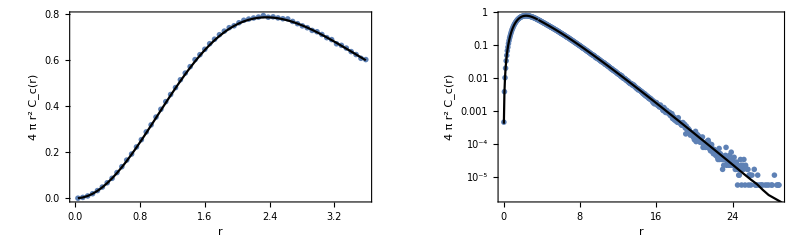

```mathematica
data=SelectFirst[simulations,#[[1]]==c&][[2]];
maxr=data[[2,5]];
dr=data[[2,7]];
MCCollisionRate=ppoints[data[[4]],dr,maxr];
exact1CRShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 Ccexact[#[[1]],c]}]& /@MCCollisionRate[[1;;60]];
exact1CR=Quiet[{#[[1]],4 Pi (#[[1]])^2 Ccexact[#[[1]],c]}]& /@MCCollisionRate[[61;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[MCCollisionRate[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1CRShallow,PlotRange->All,Joined->True,PlotStyle->Black],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[MCCollisionRate,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1CR,PlotRange->All,Joined->True,PlotStyle->Black],
ListLogPlot[exact1CRShallow,PlotRange->All,Joined->True,PlotStyle->Black],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Infinite 3D, isotropic point source, Rayleigh scattering, Chi-3 random flight - correlated emission\nCollision-rate density C_c[r], c = "<>ToString[c]]
```

## Moments

```mathematica
pc[s_]:=(ⅇ^(-s^2/4) s^2)/(2 √π)
```

### correlation emission

#### collision rate

```mathematica
m0Cc[c_]:=1/(1-c)
```

```mathematica
m2Cc[c_,s_,s2_,g_]:=s2/(1-c)^2(1+c g (2 s^2)/(s2(1-c g)))
```

#### fluence

```mathematica
m0ϕc[c_,s_]:=s/(1-c)
```

```mathematica
m2ϕc[c_,s_,s2_,s3_,g_]:=(s3 (1-c)(1-g c)+3 c s(2 g c s^2+s2(-2 g c+g+1)))/(3  (1-c)^2(1-c g))
```

```mathematica
simsC=simulations;
```

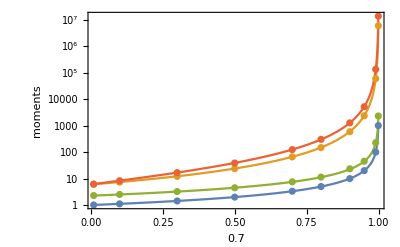

```mathematica
m0Ccs={#[[1]],#[[-1,8,1]]}&/@simsC;
m2Ccs={#[[1]],#[[-1,8,3]]}&/@simsC;
m0ϕcs={#[[1]],#[[-1,10,1]]}&/@simsC;
m2ϕcs={#[[1]],#[[-1,10,3]]}&/@simsC;
mfp=Integrate[pc[s]s,{s,0,Infinity}];
mfp2=Integrate[pc[s]s s,{s,0,Infinity}];
mfp3=Integrate[pc[s]s s s,{s,0,Infinity}];
g=0;
Show[
LogPlot[{m0Cc[c],m2Cc[c,mfp,mfp2,g],m0ϕc[c,mfp],m2ϕc[c,mfp,mfp2,mfp3,g]},{c,0.01,0.999},PlotRange->All],
ListLogPlot[{m0Ccs,m2Ccs,m0ϕcs,m2ϕcs},PlotRange->All],PlotRange->All,Frame->True,FrameLabel->{{"moments",},{c,"Chi-3 Correlated Emission 3D Rayleigh scattering\nCollision-rate density moments"}}
]
```

## Namespace

```mathematica
End[]
```

inf3DisopointRayleighscatterChi3`